```mathematica
Входные данные;
```

```mathematica
ϵ=0.001;α=10;
f[{x_,y_}]:=α(x^2-y)^2+(x-1)^2; X0={-1,-2};
(*f[{x_,y_}]:=10 x^2+7 y^2-4x y-4*5^(1/2)(5x- y)-16; X0={0,-5^(1/2)};*)

uniformMesh[left_,right_,n_]:=Table[i,{i,left,right,(right-left)/n}]
n=2;
X=X0;
points={X0};
normX={};
normF={};
fValues={f[X0]};
pArray={};
wArray={};
κArray={};
Clear[κ,ka, kap];
```

```mathematica
Метод циклического покоординатного спуска;
```

Результат получен за 107 итер.: X = {0.982538, 0.965381}

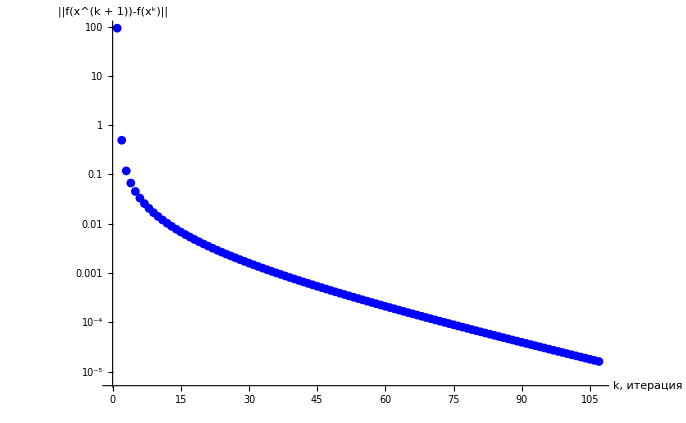

```mathematica
e=IdentityMatrix[n];
While[ True,
For[i=1,i≤n,i++,
κ = NArgMin[f[X+κ0 e[[i]]],κ0];
X=X+κ e[[i]];

];
normX=Append[normX, Norm[X-points[[-1]]]]; normF =Append[normF, Norm[f[X]-fValues[[-1]]]];
points=Append[points,X];fValues=Append[fValues,f[X]];
If[normX[[-1]]< ϵ && normF[[-1]]< ϵ, Break[], 1];
];
normX=Append[normX, Norm[X-points[[-1]]]]; normF =Append[normF, Norm[f[X]-fValues[[-1]]]];


(*Print[ToString[it]<>": норма градиента = "<>ToString[Round[norm[[-1]],0.01ϵ]]];*)
"Результат получен за "<>ToString[Length[points]-1]<> " итер.: X = "<>ToString[X]
ListLogPlot[normF,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||f(x^(k + 1))-f(x^k)||"}]
```

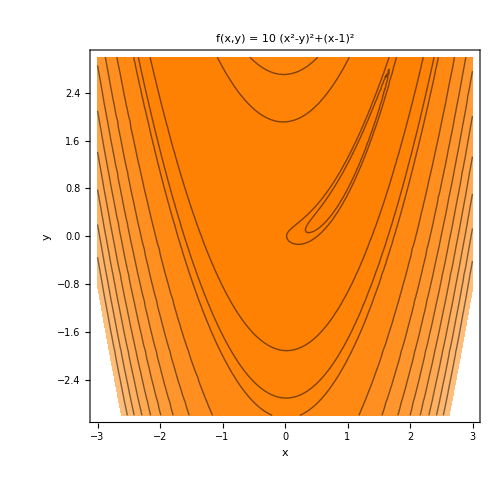

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;3]]~Join~{fValues[[1]],fValues[[3]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500]
```

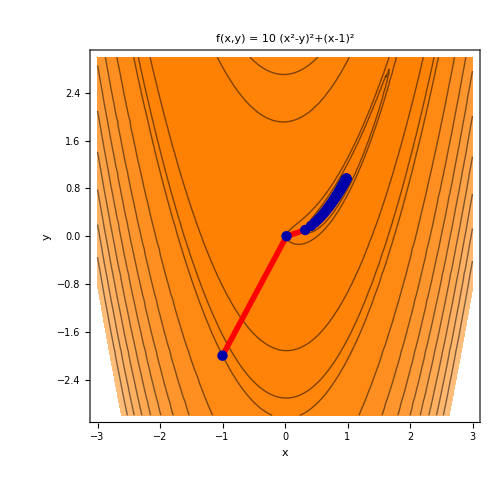

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;3]]~Join~{fValues[[1]],fValues[[3]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Red,Thickness[0.008],Line[points],Darker[Blue],PointSize[0.015],Point[points],Black}]
```

```mathematica
len=Length[normF];
gridLabel={"k","X^k","f(X^k)","||f(X^(k + 1))-f(X^k)||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,len}];gridData[[All,1]]=Table[i,{i,0,len-1}];
For[i=1,i≤len,i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],8]]<>", "<>ToString[SetAccuracy[points[[i,2]],8]]<>" )"]
(*gridData[[All,3]]=SetAccuracy[fValues,8];*)
For[i=1,i≤len,i++,gridData[[i,3]]=ToString[SetAccuracy[fValues[[i]],8]]];
gridData[[All,4]]=SetAccuracy[normF,8];
gridData={gridLabel}~Join~gridData;
Grid[gridData[[1;;3]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[len-4;;len+1]],Dividers->{Table[i->True,{i,1,1+Length[gridLabel]}],True},FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15],Background->{None,{{LightCyan,LightBlue}}}]
```

k | X^k | f(X^k) | ||f(X^(k + 1))-f(X^k)||
0 | ( -1.0000000, -2.0000000 ) | 94.0000000 | 93.0481718
1 | ( 0.0243832, 0.0005945 ) | 0.9518282 | 0.4947795
... | ... | ... | ...
102 | ( 0.9801518, 0.9606975 ) | 0.0003940 | 0.0000197
103 | ( 0.9806548, 0.9616838 ) | 0.0003742 | 0.0000187
104 | ( 0.9811446, 0.9626447 ) | 0.0003555 | 0.0000178
105 | ( 0.9816215, 0.9635809 ) | 0.0003378 | 0.0000169
106 | ( 0.9820860, 0.9644929 ) | 0.0003209 | 0.000016
107 | ( 0.9825383, 0.9653815 ) | 0.0003049 | 0.

```mathematica
Метод Хука - Дживса;
```

Результат получен за 83 итер.: X = {1.01865, 1.03825}

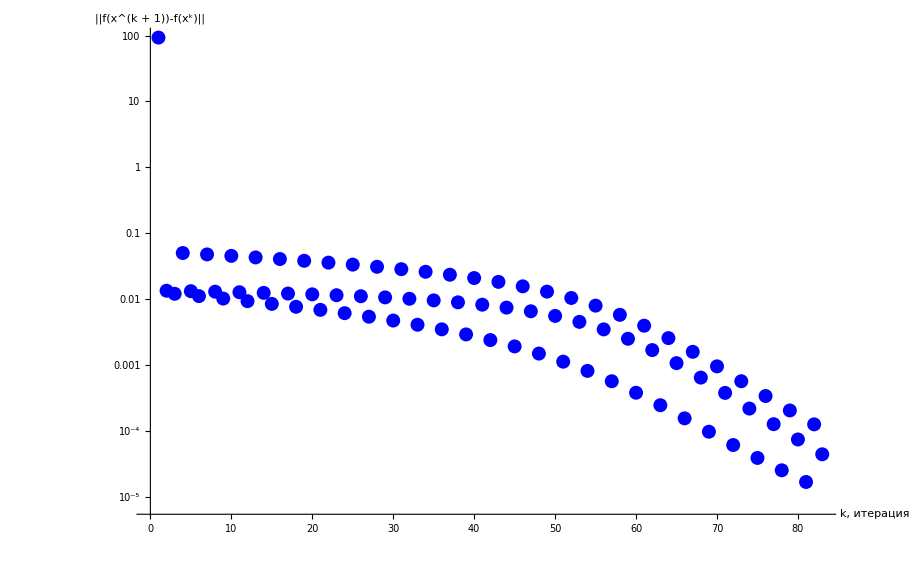

```mathematica
X=X0;
points={X0};
fValues={f[X0]};
normX={};
normF={};
Clear[κ,κ0];

e=IdentityMatrix[n];
While[ True,
κArray={};
For[i=1,i≤n,i++,
κ = NArgMin[f[X+κ0 e[[i]]],κ0]; κArray=Append[κArray,κ];
X=X+κ e[[i]];
];
u=Sum[κArray[[i]] e[[i]],{i,1,n}];
κ = NArgMin[f[X+κ0 u],κ0];
X=X+κ u;
normX=Append[normX, Norm[X-points[[-1]]]]; normF =Append[normF, Norm[f[X]-fValues[[-1]]]];
points=Append[points,X];fValues=Append[fValues,f[X]];
If[normX[[-1]]< ϵ && normF[[-1]]< ϵ , Break[], 1];
];
normX=Append[normX, Norm[X-points[[-1]]]]; normF =Append[normF, Norm[f[X]-fValues[[-1]]]];


(*Print[ToString[it]<>": норма градиента = "<>ToString[Round[norm[[-1]],0.01ϵ]]];*)
"Результат получен за "<>ToString[Length[points]-1]<> " итер.: X = "<>ToString[X]
ListLogPlot[normF,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||f(x^(k + 1))-f(x^k)||"}]
```

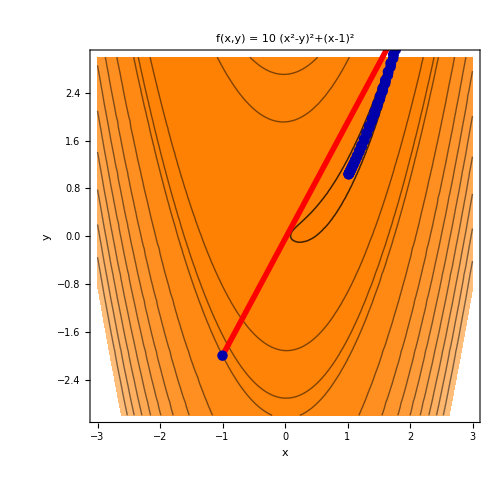

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;3]]~Join~{fValues[[1]],fValues[[3]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Red,Thickness[0.008],Line[points],Darker[Blue],PointSize[0.015],Point[points],Black}]
```

```mathematica
len=Length[normF];
gridLabel={"k","X^k","f(X^k)","||f(X^(k + 1))-f(X^k)||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,len}];gridData[[All,1]]=Table[i,{i,0,len-1}];
For[i=1,i≤len,i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],8]]<>", "<>ToString[SetAccuracy[points[[i,2]],8]]<>" )"]
(*gridData[[All,3]]=SetAccuracy[fValues,8];*)
For[i=1,i≤len,i++,gridData[[i,3]]=ToString[SetAccuracy[fValues[[i]],8]]];
gridData[[All,4]]=SetAccuracy[normF,8];
gridData={gridLabel}~Join~gridData;
Grid[gridData[[1;;3]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[len-4;;len+1]],Dividers->{Table[i->True,{i,1,1+Length[gridLabel]}],True},FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15],Background->{None,{{LightCyan,LightBlue}}}]
```

k | X^k | f(X^k) | ||f(X^(k + 1))-f(X^k)||
0 | ( -1.0000000, -2.0000000 ) | 94.0000000 | 93.1614813
1 | ( 1.9026472, 3.6687969 ) | 0.8385187 | 0.013385
... | ... | ... | ...
78 | ( 1.0284829, 1.0571543 ) | 0.0008152 | 0.0002037
79 | ( 1.0221746, 1.0483009 ) | 0.0006114 | 0.0000739
80 | ( 1.0230614, 1.0474108 ) | 0.0005375 | 0.0000167
81 | ( 1.0227594, 1.0455035 ) | 0.0005208 | 0.0001253
82 | ( 1.0179808, 1.0389721 ) | 0.0003955 | 0.000044
83 | ( 1.0186527, 1.0382539 ) | 0.0003515 | 0.

```mathematica
Метод Розенброка;
```

Результат получен за 11 итер.: X = {0.998226, 0.996384}

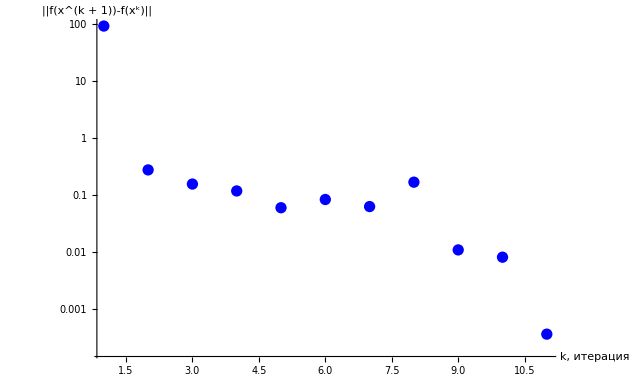

```mathematica
X=X0;
points={X0};
fValues={f[X0]};
normX={};
normF={};
Clear[κ,κ0];

e=IdentityMatrix[n];
While[ True,
κArray={};
For[i=1,i≤n,i++,
κ = NArgMin[f[X+κ0 e[[i]]],κ0]; κArray=Append[κArray,κ];
X=X+κ e[[i]];
];
normX=Append[normX, Norm[X-points[[-1]]]]; normF =Append[normF, Norm[f[X]-fValues[[-1]]]];
points=Append[points,X];fValues=Append[fValues,f[X]];
If[normX[[-1]]< ϵ || normF[[-1]]< ϵ, Break[], 1];
u=Sum[κArray[[i]] e[[i]],{i,1,n}];
u=Normalize[u];
e={u, Normalize[{u[[2]],-u[[1]]}]};
];
normX=Append[normX, Norm[X-points[[-1]]]]; normF =Append[normF, Norm[f[X]-fValues[[-1]]]];


(*Print[ToString[it]<>": норма градиента = "<>ToString[Round[norm[[-1]],0.01ϵ]]];*)
"Результат получен за "<>ToString[Length[points]-1]<> " итер.: X = "<>ToString[X]
ListLogPlot[normF,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||f(x^(k + 1))-f(x^k)||"}]
```

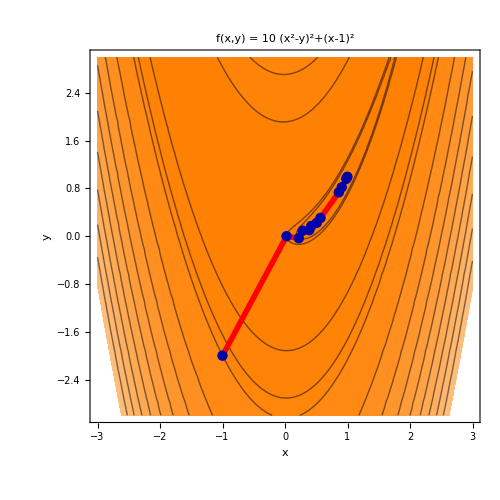

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;3]]~Join~{fValues[[1]],fValues[[3]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Red,Thickness[0.008],Line[points],Darker[Blue],PointSize[0.015],Point[points],Black}]
```

```mathematica
len=Length[normF];
gridLabel={"k","X^k","f(X^k)","||f(X^(k + 1))-f(X^k)||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,len}];gridData[[All,1]]=Table[i,{i,0,len-1}];
For[i=1,i≤len,i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],8]]<>", "<>ToString[SetAccuracy[points[[i,2]],8]]<>" )"]
(*gridData[[All,3]]=SetAccuracy[fValues,8];*)
For[i=1,i≤len,i++,gridData[[i,3]]=ToString[SetAccuracy[fValues[[i]],8]]];
gridData[[All,4]]=SetAccuracy[normF,8];
gridData={gridLabel}~Join~gridData;
Grid[gridData[[1;;3]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[len-4;;len+1]],Dividers->{Table[i->True,{i,1,1+Length[gridLabel]}],True},FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15],Background->{None,{{LightCyan,LightBlue}}}]
```

k | X^k | f(X^k) | ||f(X^(k + 1))-f(X^k)||
0 | ( -1.0000000, -2.0000000 ) | 94.0000000 | 93.0481718
1 | ( 0.0243832, 0.0005945 ) | 0.9518282 | 0.2784262
... | ... | ... | ...
6 | ( 0.5087377, 0.2254467 ) | 0.2524725 | 0.0633115
7 | ( 0.5678507, 0.3069370 ) | 0.1891609 | 0.1696024
8 | ( 0.8613005, 0.7361727 ) | 0.0195586 | 0.010997
9 | ( 0.9082024, 0.8211598 ) | 0.0085616 | 0.0081927
10 | ( 0.9809438, 0.9614927 ) | 0.0003689 | 0.0003657
11 | ( 0.9982257, 0.9963841 ) |       -6
3.2 10 | 0.

```mathematica
Метод Пауэлла;
```

Результат получен за 6 итер.: X = {1., 1.}

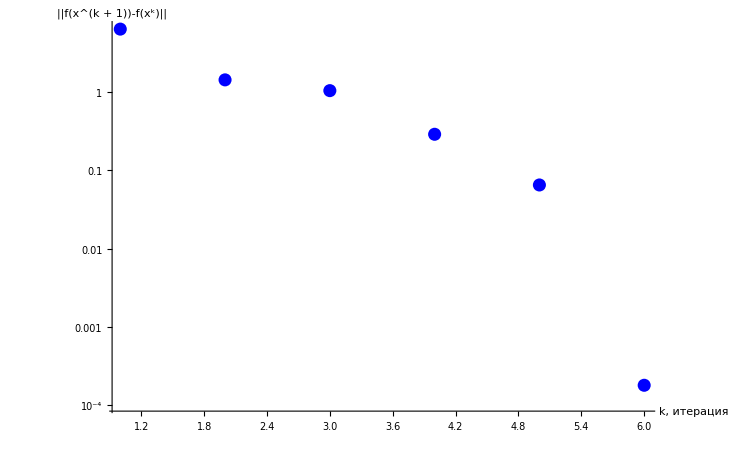

```mathematica
X=X0;
points={X0};
fValues={f[X0]};
normX={};
normF={};
Clear[κ,κ0];

e=IdentityMatrix[n];
While[ True,
κArray={};
For[i=1,i≤n,i++,
κ = NArgMin[f[X+κ0 e[[i]]],κ0]; κArray=Append[κArray,κ];
X=X+κ e[[i]];
];
u=Sum[κArray[[i]] e[[i]],{i,1,n}];
κ = NArgMin[f[X+κ0 u],κ0];
X=X+κ u;
normX=Append[normX, Norm[X-points[[-1]]]]; normF =Append[normF, Norm[f[X]-fValues[[-1]]]];
points=Append[points,X];fValues=Append[fValues,f[X]];
If[normX[[-1]]< ϵ && normF[[-1]]< ϵ, Break[], 1];
u=Normalize[u];
For[i=1,i≤ n-1,i++,
e[[i]]=e[[i+1]];
];
e[[n]]=u;
];


(*Print[ToString[it]<>": норма градиента = "<>ToString[Round[norm[[-1]],0.01ϵ]]];*)
"Результат получен за "<>ToString[Length[points]-1]<> " итер.: X = "<>ToString[X]
ListLogPlot[normX,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||f(x^(k + 1))-f(x^k)||"}]
```

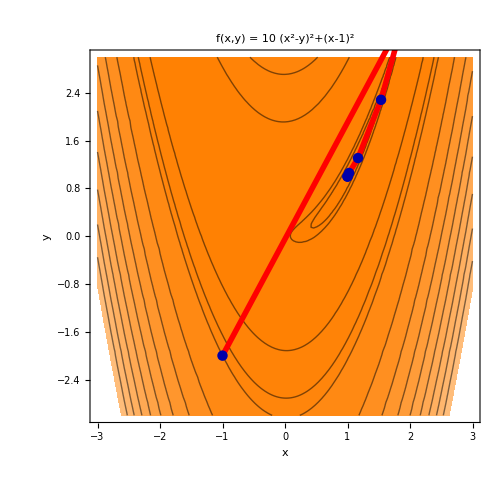

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;3]]~Join~{fValues[[1]],fValues[[3]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Red,Thickness[0.008],Line[points],Darker[Blue],PointSize[0.015],Point[points],Black}]
```

```mathematica
len=Length[normF];
gridLabel={"k","X^k","f(X^k)","||f(X^(k + 1))-f(X^k)||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,len}];gridData[[All,1]]=Table[i,{i,0,len-1}];
For[i=1,i≤len,i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],8]]<>", "<>ToString[SetAccuracy[points[[i,2]],8]]<>" )"]
(*gridData[[All,3]]=SetAccuracy[fValues,8];*)
For[i=1,i≤len,i++,gridData[[i,3]]=ToString[SetAccuracy[fValues[[i]],8]]];
gridData[[All,4]]=SetAccuracy[normF,8];
gridData={gridLabel}~Join~gridData;
Grid[gridData[[1;;3]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[len-4;;len+1]],Dividers->{Table[i->True,{i,1,1+Length[gridLabel]}],True},FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15],Background->{None,{{LightCyan,LightBlue}}}]
```

k | X^k | f(X^k) | ||f(X^(k + 1))-f(X^k)||
0 | ( -1.0000000, -2.0000000 ) | 94.0000000 | 93.1614813
1 | ( 1.9026472, 3.6687969 ) | 0.8385187 | 0.4927988
... | ... | ... | ...
0 | ( -1.0000000, -2.0000000 ) | 94.0000000 | 93.1614813
1 | ( 1.9026472, 3.6687969 ) | 0.8385187 | 0.4927988
2 | ( 1.5366917, 2.2854726 ) | 0.3457199 | 0.287922
3 | ( 1.1682268, 1.3104422 ) | 0.0577979 | 0.0564347
4 | ( 1.0252531, 1.0596617 ) | 0.0013632 | 0.0013632
5 | ( 0.9999100, 0.9998450 ) |      -7
0. 10 | 1.×10^-8